```mathematica
projectDir = "/Users/pwrzosek/Documents/GitHub/AvoidedQP/t-J_model";
plotsDir ="./plots/";
dataDir="./data/";
SetDirectory[projectDir];
Off[ToExpression::sntx];
Off[ToExpression::sntxi];
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Definitions - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

(* Read Lehmann's representation of the Green's function from a file 'filename' *)
ReadData[filename_]:=(
stream = OpenRead[filename];
n = ToExpression[Read[stream, Word]];
momentum=Table[0.0,n];
energy=Table[{},n];
weight=Table[{},n];
doMomentum=True;
doEnergy=True;
doWeight=True;
in = 1;
While[in≤ n,(
If[doMomentum,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
momentum[[in]]=token;
doMomentum=False;
),
If[doEnergy,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
While[NumberQ[token],(
AppendTo[energy[[in]],token];
token=ToExpression[Read[stream, Word]];
)];
doEnergy=False;
),
If[doWeight,(
token=ToExpression[Read[stream, Word]];
While[!NumberQ[token],token=ToExpression[Read[stream, Word]]];
While[NumberQ[token],(
AppendTo[weight[[in]],token];
token=ToExpression[Read[stream, Word]];
)];
doWeight=False;
),(
doMomentum=True;
doEnergy=True;
doWeight=True;
in++;
)];
];
];
)];
Close[stream];

{momentum, energy, weight}
);

(* Get exact representation of possible momenta in units of π *)
getMomentumInPi[momentum_]:= Round[momentum*(Length[momentum]-1)/(Pi)]/(Length[momentum]-1);

(* Calculate spectral function A(k,ω) from Lehmann's representation of the Green's function *)
calculate[momentum_,energy_,weight_]:=(
ωMin=Min[energy];
ωMax=Max[energy];
iδ=0.05I;
ωSet=Table[ω, {ω,ωMin-1,ωMax-1,0.01}];
kSet=getMomentumInPi[momentum]*Pi;
spectrum=Table[{kSet[[kDim]],ωSet[[ωDim]],-Im[Total[weight[[kDim]]/(ωSet[[ωDim]]+iδ-energy[[kDim]])]]/Pi},{ωDim,1,Length[ωSet]},{kDim,1,Length[kSet]}];

Flatten[spectrum,1]
);

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Definitions - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Listing Files - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

files=FileNames["lehmann_*.txt",dataDir];
TableForm[Transpose[{Table[n,{n,Length[files]}],files}]]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Listing Files - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

1 | ./data/lehmann_l=12_t=1.0_J=0.4_m=1.0_.txt
2 | ./data/lehmann_l=12_t=1.0_J=1.0_m=1.0_.txt
3 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.0_.txt
4 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.1_.txt
5 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.2_.txt
6 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.3_.txt
7 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.4_.txt
8 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.5_.txt
9 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.6_.txt
10 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.7_.txt
11 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.8_.txt
12 | ./data/lehmann_l=14_t=1.0_J=0.4_m=0.9_.txt
13 | ./data/lehmann_l=14_t=1.0_J=0.4_m=1.0_.txt
14 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.0_.txt
15 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.2_.txt
16 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.4_.txt
17 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.6_.txt
18 | ./data/lehmann_l=14_t=1.0_J=1.0_m=0.8_.txt
19 | ./data/lehmann_l=14_t=1.0_J=1.0_m=1.0_.txt
20 | ./data/lehmann_l=8_t=1.0_J=1.0_m=1.0_.txt

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Spectral Function - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
whichFiles={1};
A={};
Do[(
filename=files[[it]];
{momentum,energy,weight}=ReadData[filename];
AppendTo[A,calculate[momentum,energy,weight]];
),{it,whichFiles}]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Spectral Function - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Plot Setup - BEGIN *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)

FrameTicksFontSize=18;
LegendFontSize=14;
colors="DeepSeaColors";
SetOptions[ListDensityPlot,InterpolationOrder->0,AspectRatio->1/2,ImageSize->800,ColorFunction->colors,FrameTicksStyle->Directive[FrameTicksFontSize,Black],FrameTicks-> {Automatic,{getMomentumInPi[momentum]*Pi,Automatic}},PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[LegendFontSize, Black]],Right],FrameLabel-> {Style["k",FrameTicksFontSize,Black],Style["ω",FrameTicksFontSize,Black]},LabelStyle->Directive[FrameTicksFontSize,Black],FrameStyle->Directive[Black,Thick]]

(* -------------------------------------------------------------------------------------------------------------------------------- *)
(* Plot Setup - END *)
(* -------------------------------------------------------------------------------------------------------------------------------- *)
```

{AlignmentPoint→Center,AspectRatio→1/2,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→DeepSeaColors,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→True,FrameLabel→{k,ω},FrameStyle→Directive[GrayLevel[0],Thickness[Large]],FrameTicks→{Automatic,{{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6,2 π},Automatic}},FrameTicksStyle→Directive[18,GrayLevel[0]],GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→800,ImageSizeRaw→Automatic,InterpolationOrder→0,LabelStyle→Directive[18,GrayLevel[0]],LightingAngle→None,MaxPlotPoints→Automatic,Mesh→None,MeshFunctions→{#1&,#2&},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→Placed[BarLegend[Automatic,LabelStyle→Directive[14,GrayLevel[0]]],Right],PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},VertexColors→Automatic}

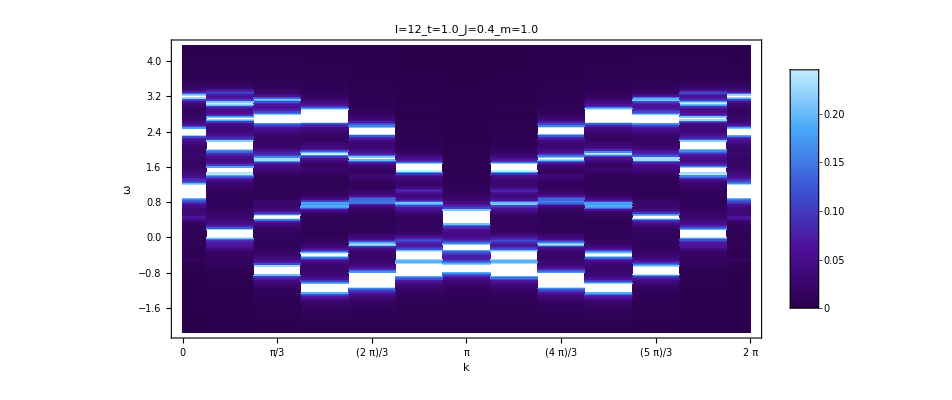

```mathematica
plots=Table[ListDensityPlot[A[[it]],PlotLabel->StringJoin[Characters[files[[whichFiles[[it]]]]][[16;;-6]]]],{it,1,Length[A]}];
TableForm[plots]
```

```mathematica
Do[(
Export[StringJoin[plotsDir,StringJoin[Characters[files[[whichFiles[[it]]]]][[16;;-5]]],".png"],plots[[it]],ImageResolution->200];
),{it,1,Length[plots]}]
```